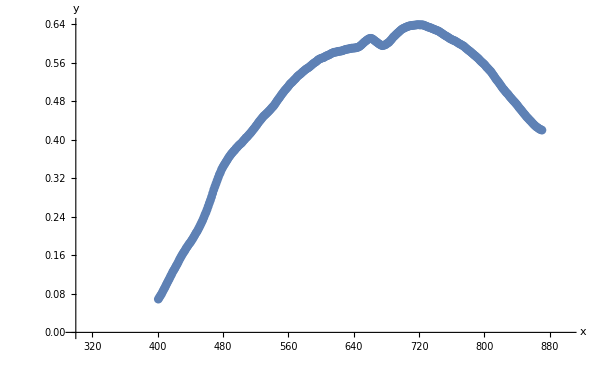

{a→1.81916×10^16,b→3660.26}

```mathematica
SetDirectory[NotebookDirectory[]];
mydata=Import["C:\\Users\\abrah_nwf804r\\Documents\\cuantica\\lampara.csv"];
Im1=ListPlot[mydata,PlotRange->{{300,900},All},
ImageSize->600,AxesLabel->{x,y},PlotMarkers->{Automatic,9}]
fit=FindFit[mydata,a/(x^5(ⅇ^(b/x) -1)),{a,b},x, Gradient->"FiniteDifference"]
```

{a→1.81916×10^16,b→3660.26}

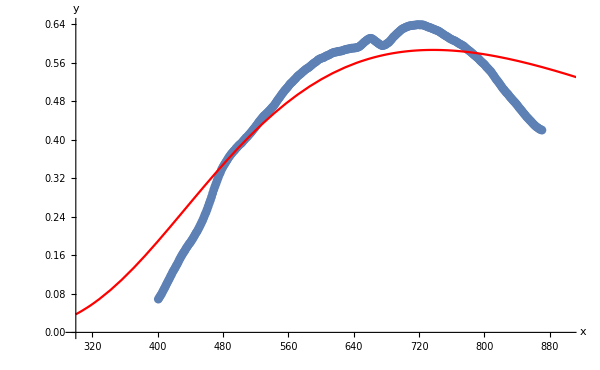

```mathematica
{a->1.8191560320156348*^16,b->3660.257041645851}


Im2=Plot[(1.8191560320156348*^16)/(x^5(ⅇ^(3660.257041645851/x) -1)),{x,300,1000},PlotStyle->Red];
Show[Im1,Im2]
```

```mathematica
ListPlot[mydata,PlotRange->{{300,900}All},ImageSize->300,1000]
```

ListPlot::nonopt: Options expected (instead of 1000) beyond position 1 in ListPlot[{{400.958,0.0691523},{402.315,0.072969},{403.671,0.0766869},{405.028,0.0802733},{406.385,0.0848796},{407.741,0.0893543},{409.097,0.0934671},{410.454,0.0983695},{411.81,0.102943},{413.167,0.107418},«337»},PlotRange→{{300 All,900 All}},ImageSize→300,1000]. An option must be a rule or a list of rules.

ListPlot[{{400.958,0.0691523},{402.315,0.072969},{403.671,0.0766869},{405.028,0.0802733},{406.385,0.0848796},{407.741,0.0893543},{409.097,0.0934671},{410.454,0.0983695},{411.81,0.102943},{413.167,0.107418},{414.523,0.111662},{415.88,0.116499},{417.236,0.12071},{418.593,0.125678},{419.95,0.129462},{421.306,0.133345},{422.662,0.137819},{424.019,0.141735},{425.375,0.146242},{426.732,0.151046},{428.088,0.155192},{429.445,0.159304},{430.801,0.16322},{432.158,0.166872},{433.514,0.170162},{434.871,0.174538},{436.227,0.177664},{437.584,0.18125},{438.94,0.184606},{440.297,0.187271},{441.654,0.191088},{443.01,0.194477},{444.366,0.198425},{445.723,0.202439},{447.079,0.206651},{448.436,0.209941},{449.792,0.214449},{451.149,0.218825},{452.505,0.223464},{453.862,0.228202},{455.219,0.232973},{456.575,0.238467},{457.931,0.244357},{459.288,0.249555},{460.644,0.255576},{462.001,0.262124},{463.357,0.268704},{464.714,0.274857},{466.07,0.281602},{467.427,0.289071},{468.784,0.296441},{470.14,0.302824},{471.496,0.30901},{472.853,0.315393},{474.209,0.321611},{475.566,0.32783},{476.922,0.332568},{478.279,0.338358},{479.635,0.342636},{480.992,0.346781},{482.349,0.350368},{483.705,0.354283},{485.061,0.357804},{486.418,0.361752},{487.774,0.36524},{489.131,0.368234},{490.487,0.371557},{491.844,0.373959},{493.2,0.37692},{494.557,0.378993},{495.913,0.382349},{497.27,0.384422},{498.626,0.387218},{499.983,0.389554},{501.339,0.391561},{502.696,0.393404},{504.052,0.396201},{505.409,0.399129},{506.765,0.401268},{508.122,0.404492},{509.478,0.406038},{510.835,0.408868},{512.191,0.411467},{513.548,0.413902},{514.904,0.416797},{516.261,0.419759},{517.617,0.42272},{518.974,0.425418},{520.331,0.428807},{521.687,0.43157},{523.043,0.435058},{524.4,0.438217},{525.756,0.440849},{527.113,0.44381},{528.469,0.446673},{529.826,0.449502},{531.182,0.451509},{532.539,0.453648},{533.895,0.455918},{535.252,0.458156},{536.609,0.460623},{537.965,0.462959},{539.322,0.465657},{540.678,0.468256},{542.034,0.470658},{543.391,0.473817},{544.747,0.477173},{546.104,0.480759},{547.46,0.484017},{548.817,0.487044},{550.173,0.490268},{551.53,0.493723},{552.887,0.496717},{554.243,0.499711},{555.6,0.502935},{556.956,0.505239},{558.312,0.508068},{559.669,0.510602},{561.025,0.513826},{562.382,0.516721},{563.738,0.518729},{565.095,0.520867},{566.451,0.523499},{567.808,0.525737},{569.164,0.527908},{570.521,0.530869},{571.878,0.53314},{573.234,0.534982},{574.591,0.536693},{575.947,0.538601},{577.303,0.541003},{578.66,0.542846},{580.016,0.54482},{581.373,0.546794},{582.729,0.548275},{584.086,0.54969},{585.442,0.551104},{586.799,0.55321},{588.156,0.554987},{589.512,0.557158},{590.869,0.5591},{592.225,0.560712},{593.582,0.562127},{594.938,0.563903},{596.294,0.566338},{597.651,0.56749},{599.007,0.568839},{600.364,0.56976},{601.72,0.57055},{603.077,0.571142},{604.433,0.572293},{605.79,0.574202},{607.147,0.574926},{608.503,0.576077},{609.86,0.576669},{611.216,0.578282},{612.572,0.579663},{613.929,0.580618},{615.285,0.581736},{616.642,0.582394},{617.998,0.582427},{619.355,0.583052},{620.711,0.583908},{622.068,0.58427},{623.425,0.584401},{624.781,0.584862},{626.138,0.585356},{627.494,0.586408},{628.851,0.587264},{630.207,0.587955},{631.563,0.588613},{632.92,0.588876},{634.276,0.589238},{635.633,0.589896},{636.989,0.590587},{638.346,0.59085},{639.702,0.590686},{641.059,0.591278},{642.416,0.591278},{643.772,0.591903},{645.129,0.59266},{646.485,0.593515},{647.841,0.595292},{649.198,0.597036},{650.554,0.599339},{651.911,0.601478},{653.267,0.603847},{654.624,0.605196},{655.98,0.607466},{657.337,0.608815},{658.693,0.610295},{660.05,0.611184},{661.407,0.611151},{662.763,0.610131},{664.12,0.608552},{665.476,0.606742},{666.832,0.604735},{668.189,0.60332},{669.545,0.601313},{670.902,0.599701},{672.258,0.598253},{673.615,0.596937},{674.971,0.595917},{676.328,0.596542},{677.685,0.597069},{679.041,0.598056},{680.398,0.599898},{681.754,0.601543},{683.111,0.60286},{684.467,0.605656},{685.823,0.608058},{687.18,0.610855},{688.536,0.613882},{689.893,0.61579},{691.249,0.618225},{692.606,0.620495},{693.962,0.622634},{695.319,0.624542},{696.676,0.626845},{698.032,0.628754},{699.389,0.630629},{700.745,0.631715},{702.101,0.632768},{703.458,0.63415},{704.814,0.634873},{706.171,0.635861},{707.527,0.636815},{708.884,0.637177},{710.24,0.637802},{711.597,0.637637},{712.954,0.638427},{714.31,0.638526},{715.667,0.638855},{717.023,0.639052},{718.38,0.639578},{719.736,0.639414},{721.092,0.638953},{722.449,0.639348},{723.805,0.639118},{725.162,0.638953},{726.518,0.637835},{727.875,0.636913},{729.231,0.636255},{730.588,0.634841},{731.945,0.634215},{733.301,0.63359},{734.658,0.632669},{736.014,0.631452},{737.37,0.630728},{738.727,0.629675},{740.083,0.628622},{741.44,0.627964},{742.796,0.626812},{744.153,0.625957},{745.509,0.624279},{746.866,0.622765},{748.222,0.621252},{749.579,0.619574},{750.936,0.618028},{752.292,0.616547},{753.649,0.615165},{755.005,0.614145},{756.361,0.612204},{757.718,0.610592},{759.074,0.609736},{760.431,0.60819},{761.787,0.607137},{763.144,0.606545},{764.5,0.60513},{765.857,0.603847},{767.214,0.602333},{768.57,0.600622},{769.927,0.599504},{771.283,0.598319},{772.639,0.59674},{773.996,0.59572},{775.352,0.593976},{776.709,0.591673},{778.065,0.589764},{779.422,0.587725},{780.778,0.585948},{782.135,0.584303},{783.491,0.582394},{784.848,0.580322},{786.205,0.578413},{787.561,0.576242},{788.918,0.574629},{790.274,0.572392},{791.63,0.570484},{792.987,0.568345},{794.343,0.565647},{795.7,0.563377},{797.056,0.561271},{798.413,0.559264},{799.769,0.557158},{801.126,0.554625},{802.483,0.551499},{803.839,0.549295},{805.196,0.54663},{806.552,0.544261},{807.909,0.541958},{809.265,0.538569},{810.621,0.535213},{811.978,0.532087},{813.334,0.528369},{814.691,0.52521},{816.047,0.522512},{817.404,0.519452},{818.76,0.516195},{820.117,0.513004},{821.474,0.509516},{822.83,0.506423},{824.187,0.503923},{825.543,0.50083},{826.899,0.498132},{828.256,0.495993},{829.612,0.493098},{830.969,0.489939},{832.325,0.487438},{833.682,0.484741},{835.038,0.48201},{836.395,0.479739},{837.751,0.477173},{839.108,0.474376},{840.465,0.471645},{841.821,0.468322},{843.178,0.46546},{844.534,0.462926},{845.89,0.459998},{847.247,0.457004},{848.603,0.454273},{849.96,0.451575},{851.316,0.448449},{852.673,0.446146},{854.029,0.443711},{855.386,0.441079},{856.743,0.438875},{858.099,0.436243},{859.456,0.433841},{860.812,0.431406},{862.168,0.429366},{863.525,0.427129},{864.881,0.425813},{866.238,0.424036},{867.594,0.422292},{868.951,0.421502},{870.307,0.420384}},PlotRange→{{300 All,900 All}},ImageSize→300,1000]